```mathematica
Clear[vLikelihood]
```

```mathematica
vPriorTriangular[θ_] := If[θ≤ 0.5,4θ,4-4θ]
vPriorFlat[θ_] := PDF[UniformDistribution[{0,0.45}],θ]
vPrior[θ_]:=If[θ≤0.45,vPriorFlat[θ],0]
```

```mathematica
vIsInteger[z_]:=If[IntegerQ[Rationalize[z]],1,0]
```

```mathematica
vLikelihood[θ_,z_]=Likelihood[BinomialDistribution[100,θ],{z}]*vPrior[θ]
```

If[θ≤0.45,vPriorFlat[θ],0] (Piecewise[{{(1-θ)^(100-z) θ^z Binomial[100,z], 0≤z≤100}, {0, True}}])

```mathematica
vLikelihood1[θ_]:=Likelihood[BinomialDistribution[100,θ],{40}]
```

```mathematica
vNumerator[θ_] := vPrior[θ]*vLikelihood1[θ]
```

```mathematica
cDenominator = NIntegrate[vNumerator[θ],{θ,0,1}];
```

```mathematica
vPosterior[θ_] := vPrior[θ]*vLikelihood1[θ]/cDenominator;
```

```mathematica
vPdata[z_] := NIntegrate[vLikelihood[θ,z],{θ,0,1}]
```

```mathematica
cTestIntegral = NIntegrate[vPdata[z],{z,0,100},MinRecursion->8];
```

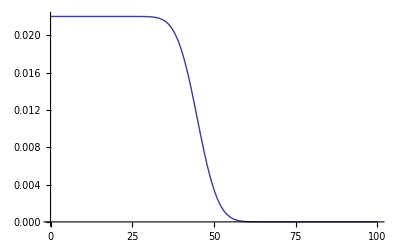

```mathematica
vPData=Table[vPdata[z],{z,0,100}];
vData = Range[0,100];
ListLinePlot[Thread[{vData,vPData}]]
```

```mathematica
data = Thread[{vData,vPData}];
```

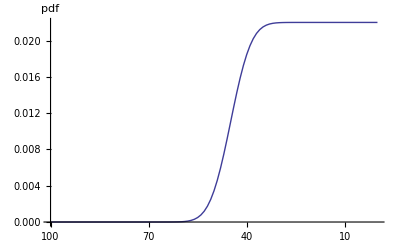

```mathematica
d=Transpose@data;
g3=ListLinePlot[Transpose@{Reverse@d[[1]],d[[2]]},Ticks->{Transpose@{Range[0,100,10],Range[100,0,-10]},Automatic},BaseStyle->{FontSize->16},AxesLabel->{"",pdf}]
```

```mathematica
pData=Rotate[g3,90 Degree]
```

-Graphics-

```mathematica
LineConstantData =Table[{x,40},{x,0,1,0.1}];
```

```mathematica
padding={{100,30},{30,30}};
pJointDataTheta=Show[ContourPlot[vLikelihood[θ,z],{θ,0,1},{z,0,100},PlotRange->{{0,1},{0,100},{0,1}},Mesh->None,ContourShading->{White},ContourStyle->{Black},FrameLabel->{θ,"Number of sample voting conservatively"},BaseStyle->{FontSize->16},ImagePadding->padding],ListLinePlot[LineConstantData]];
pPosterior = Plot[vPosterior[θ],{θ,0,1},PlotRange->Full,PlotStyle->{Black},ImagePadding->padding,BaseStyle->{FontSize->16},AxesLabel->{θ,"pdf"}];
Show[GraphicsGrid[{{pJointDataTheta,pData},{pPosterior,}}],ImageSize->Large]
```

-Graphics-